```mathematica
conductanciaBE[θ_]:=(((PlanckConstant/(2π))^2 velocidad^2)/(ancho*largo*altura*BoltzmannConstant*θ^2))Sum[((2π*n)/largo)*amplitudWSim[(2π*n)/largo*ancho,0.0, 0.0]^2, {n,1,30}]
```

```mathematica
conductanciaBE[θ_, y_]:=Sum[(PlanckConstant/(2π)*velocidad^2)/(largo*altura*ancho*Δθ)*largo*(2π*n/largo)*amplitudWSim[2π*n*ancho/largo,y,0.0]^2* (distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,θ] -distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,θ-Δθ] ), {n, 1, 30}];
```

```mathematica
conductanciaBE[1,0]
```

59.3421

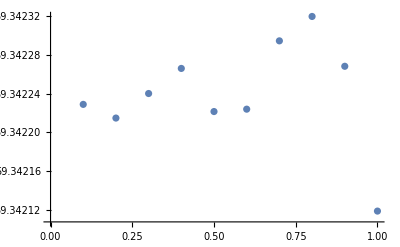

```mathematica
ListPlot[Table[{θ,conductanciaBE[θ,0.0]}, {θ,0.1,1,0.1}]]
```

FindRoot::precw: The precision of the argument function (√(-4.17327×10^-8+w) (2.78218×10^-8+w)^2 Cosh[(√(4.17327×10^-8+w))/2] Sin[(√(-4.17327×10^-8+w))/2]+(-2.78218×10^-8+w)^2 √(4.17327×10^-8+w) Cos[(√(-4.17327×10^-8+w))/2] Sinh[(√(4.17327×10^-8+w))/2]==0) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

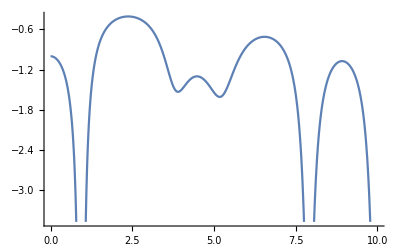

```mathematica
Plot[amplitudWSim[k,0.0, 0.0],{k, 0,10}]
```

FindRoot::precw: The precision of the argument function (√(-0.0355727+w) (0.0237151+w)^2 Cosh[(√(0.0355727+w))/2] Sin[(√(-0.0355727+w))/2]+(-0.0237151+w)^2 √(0.0355727+w) Cos[(√(-0.0355727+w))/2] Sinh[(√(0.0355727+w))/2]==0) is less than WorkingPrecision (20.).

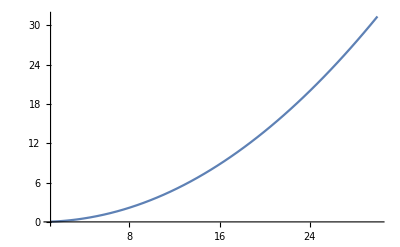

```mathematica
Plot[frecuenciaωSimPositivo[2π*n*ancho/largo,0],{n,1,30}]
```